```mathematica
1
```

1

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→SparseArray[…],Entrance Vertices and Flows→{{1,400}},Exit Vertices and Terminal Costs→{{9,0}},Switching Costs→{}|>

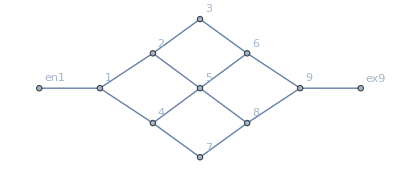

Switching costs simplified in 0.033619 seconds.

Balance equations solved in 0.002819 seconds.

TripleClean took 0.011855 seconds.

TripleClean again (with some more equalities) took 0.009679 seconds.

```mathematica
Data=DataG["Grid0303"]
d2e1=Data2Equations[Data];
d2e=MFGPreprocessing[d2e1];
```

```mathematica
(nn=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

MFGSS: Calculated the cost plus currents for the flow in 0.000243 seconds.

MFGS: Selecting inequalities by transition flow took 0.009338 seconds. 52

MFGSS: Simplifying inequalities by transition flow took 0.062582 seconds.

Final: {0,135,68}

Final: Iterative DNF convertion on 60 disjunctions took 0.181605 seconds to terminate.

Final: Reducing (each alternative)... 17 of them.

Final: Reducing (each alternative), returned 15 of them, took 0.023846 seconds to terminate.

Final: (j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0&&j[4,5,2]==0)||(j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0&&j[4,5,2]+j[4,5,8]==0)||(j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&j[4,5,2]==0&&j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&j[4,5,2]==0&&j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100)

Now: 11:54:22GMT+3TimeObject[{11,54,22.059385},Instant,3.]The new rules are: <|j[en1,1]→400,j[1,en1]→0,j[ex9,9]→0,u[1,en1]→600,j[9,ex9]→400,j[1,2]→j[1,2,3]+j[1,2,5],j[1,4]→j[1,4,5]+j[1,4,7],j[2,3]→j[2,3,6],j[2,5]→j[2,5,4]+j[2,5,6]+j[2,5,8],j[3,6]→j[2,3,6],j[4,5]→j[4,5,2]+j[4,5,6]+j[4,5,8],j[4,7]→j[4,7,8],j[5,6]→j[5,6,3]+j[5,6,9],j[5,8]→j[5,8,7]+j[5,8,9],j[6,9]→j[2,3,6]-j[3,6,5]+j[5,6,9],j[7,8]→j[4,7,8],j[8,9]→200+j[6,9,8],j[2,1]→-200+j[1,2,3]+j[1,2,5],j[4,1]→-200+j[1,4,5]+j[1,4,7],j[3,2]→-100+j[2,3,6],j[5,2]→-100+j[2,5,4]+j[2,5,6]+j[2,5,8],j[6,3]→-100+j[2,3,6],j[5,4]→-100+j[4,5,2]+j[4,5,6]+j[4,5,8],j[7,4]→-100+j[4,7,8],j[6,5]→-100+j[5,6,3]+j[5,6,9],j[8,5]→-100+j[5,8,7]+j[5,8,9],j[9,6]→-200+j[2,3,6]-j[3,6,5]+j[5,6,9],j[8,7]→-100+j[4,7,8],j[9,8]→j[6,9,8],u[ex9,9]→0,u[9,ex9]→0,j[3,2,5]→-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8],j[3,6,9]→j[2,3,6]-j[3,6,5],j[4,1,2]→-200+j[1,4,5]+j[1,4,7],j[5,2,1]→-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8],j[5,2,3]→-j[1,2,3]+j[2,3,6],j[5,4,7]→-j[1,4,7]+j[4,7,8],j[6,3,2]→-100+j[2,3,6],j[6,5,8]→-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9],j[6,9,ex9]→j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8],j[7,4,1]→-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8],j[7,4,5]→-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8],j[7,8,9]→200-j[5,8,9]+j[6,9,8],j[8,5,2]→-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2],j[8,5,4]→-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2],j[8,5,6]→-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9],j[8,7,4]→-100+j[4,7,8],j[8,9,6]→-200+j[2,3,6]-j[3,6,5]+j[5,6,9],j[8,9,ex9]→400-j[2,3,6]+j[3,6,5]-j[5,6,9]+j[6,9,8],j[9,6,3]→-100+j[2,3,6]-j[5,6,3],j[9,6,5]→-100-j[3,6,5]+j[5,6,3]+j[5,6,9],j[9,8,5]→100-j[4,7,8]+j[5,8,7]+j[6,9,8],j[9,8,7]→-100+j[4,7,8]-j[5,8,7],j[en1,1,2]→200+j[1,2,3]+j[1,2,5]-j[1,4,5]-j[1,4,7],j[en1,1,4]→200-j[1,2,3]-j[1,2,5]+j[1,4,5]+j[1,4,7],j[ex9,9,6]→0,j[ex9,9,8]→0,u[1,2]→400,u[1,4]→400,u[2,1]→600,u[2,5]→300,u[3,6]→200,u[4,5]→300,u[5,2]→400,u[5,8]→200,u[6,3]→300,u[6,9]→0,u[7,4]→400,u[8,5]→300,u[8,7]→300,u[8,9]→0,u[9,6]→200,u[9,8]→200,u[en1,1]→600,j[4,1,en1]→0,j[2,1,en1]→0,j[3,2,1]→-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8],j[5,4,1]→-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8],j[6,5,4]→-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2],u[2,3]→300,u[3,2]→400,u[4,1]→600,u[4,7]→300,u[5,4]→400,u[5,6]→200,u[6,5]→300,u[7,8]→200,j[2,1,4]→-200+j[1,2,3]+j[1,2,5],j[7,8,5]→-200+j[4,7,8]+j[5,8,9]-j[6,9,8]|>{0,0,4}

BooleanConvert done. Simplifying...

Simplifying done. TripleClean...

MFGSS: (Possibly) Multiple solutions:
(j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0&&(j[4,5,2]==0||j[4,5,2]+j[4,5,8]==0))||(j[4,5,2]==0&&((j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100)))

MFGSS: Picked one solution: <|j[2,5,6]→0,j[2,5,8]→100,j[4,5,2]→0,j[4,5,6]→100,j[4,5,8]→0|>

{0.438696,Null}

```mathematica
ReplaceSolution[(j[2,5,6]==0||j[6,5,2]==0)&&(j[3,6,5]==0||j[5,6,3]==0)&&(j[4,5,2]==0||j[2,5,4]==0)&&(j[5,6,3]==0||j[3,6,5]==0)&&(j[6,5,2]==0||j[2,5,6]==0)&&(j[6,9,8]==0||200+j[6,9,8]==0)&&(200+j[6,9,8]==0||j[6,9,8]==0)&&(-100+j[2,3,6]==0||j[2,3,6]==0)&&(j[2,3,6]==0||-100+j[2,3,6]==0)&&(-100+j[4,7,8]==0||j[4,7,8]==0)&&(j[4,7,8]==0||-100+j[4,7,8]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||j[1,2,3]+j[1,2,5]==0)&&(j[1,2,3]+j[1,2,5]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||j[1,4,5]+j[1,4,7]==0)&&(j[1,4,5]+j[1,4,7]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-100+j[5,6,3]+j[5,6,9]==0||j[5,6,3]+j[5,6,9]==0)&&(j[5,6,3]+j[5,6,9]==0||-100+j[5,6,3]+j[5,6,9]==0)&&(-100+j[5,8,7]+j[5,8,9]==0||j[5,8,7]+j[5,8,9]==0)&&(j[5,8,7]+j[5,8,9]==0||-100+j[5,8,7]+j[5,8,9]==0)&&(j[5,8,9]==0||100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0)&&(100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0||j[5,8,9]==0)&&(j[5,6,9]==0||-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[6,9,8]==0)&&(-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0||j[5,6,9]==0)&&(j[5,8,7]==0||-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0)&&(-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0||j[5,8,7]==0)&&(j[6,9,8]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(j[2,3,6]-j[3,6,5]==0||-100+j[2,3,6]-j[5,6,3]==0)&&(-100+j[2,3,6]-j[5,6,3]==0||j[2,3,6]-j[3,6,5]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(-100+j[4,7,8]-j[5,8,7]==0||200-j[5,8,9]+j[6,9,8]==0)&&(200-j[5,8,9]+j[6,9,8]==0||-100+j[4,7,8]-j[5,8,7]==0)&&(j[1,2,5]==0||-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[1,4,5]==0||-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0)&&(-j[1,2,3]+j[2,3,6]==0||-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-j[1,2,3]+j[2,3,6]==0)&&(-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[1,2,5]==0)&&(-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-j[1,4,7]+j[4,7,8]==0)&&(-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0||j[1,4,5]==0)&&(-j[1,4,7]+j[4,7,8]==0||-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0||j[2,5,8]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[2,3,6]-j[3,6,5]+j[5,6,9]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[1,2,3]==0||-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0)&&(j[1,4,7]==0||-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0)&&(-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0||j[1,2,3]==0)&&(-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0||j[1,4,7]==0)&&(j[4,5,6]==0||-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0)&&(-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0||-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0)&&(-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0||-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0)&&(-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0||j[4,5,6]==0)&&(j[4,5,8]==0||-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0)&&(-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0||j[4,5,8]==0),{j[2,5,4]->0}]
```

$Aborted

```mathematica
Head[(j[2,5,6]==0||j[6,5,2]==0)&&(j[3,6,5]==0||j[5,6,3]==0)&&(j[4,5,2]==0||j[2,5,4]==0)&&(j[5,6,3]==0||j[3,6,5]==0)&&(j[6,5,2]==0||j[2,5,6]==0)&&(j[6,9,8]==0||200+j[6,9,8]==0)&&(200+j[6,9,8]==0||j[6,9,8]==0)&&(-100+j[2,3,6]==0||j[2,3,6]==0)&&(j[2,3,6]==0||-100+j[2,3,6]==0)&&(-100+j[4,7,8]==0||j[4,7,8]==0)&&(j[4,7,8]==0||-100+j[4,7,8]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||j[1,2,3]+j[1,2,5]==0)&&(j[1,2,3]+j[1,2,5]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||j[1,4,5]+j[1,4,7]==0)&&(j[1,4,5]+j[1,4,7]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-100+j[5,6,3]+j[5,6,9]==0||j[5,6,3]+j[5,6,9]==0)&&(j[5,6,3]+j[5,6,9]==0||-100+j[5,6,3]+j[5,6,9]==0)&&(-100+j[5,8,7]+j[5,8,9]==0||j[5,8,7]+j[5,8,9]==0)&&(j[5,8,7]+j[5,8,9]==0||-100+j[5,8,7]+j[5,8,9]==0)&&(j[5,8,9]==0||100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0)&&(100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0||j[5,8,9]==0)&&(j[5,6,9]==0||-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[6,9,8]==0)&&(-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0||j[5,6,9]==0)&&(j[5,8,7]==0||-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0)&&(-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0||j[5,8,7]==0)&&(j[6,9,8]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(j[2,3,6]-j[3,6,5]==0||-100+j[2,3,6]-j[5,6,3]==0)&&(-100+j[2,3,6]-j[5,6,3]==0||j[2,3,6]-j[3,6,5]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(-100+j[4,7,8]-j[5,8,7]==0||200-j[5,8,9]+j[6,9,8]==0)&&(200-j[5,8,9]+j[6,9,8]==0||-100+j[4,7,8]-j[5,8,7]==0)&&(j[1,2,5]==0||-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[1,4,5]==0||-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0)&&(-j[1,2,3]+j[2,3,6]==0||-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-j[1,2,3]+j[2,3,6]==0)&&(-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[1,2,5]==0)&&(-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-j[1,4,7]+j[4,7,8]==0)&&(-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0||j[1,4,5]==0)&&(-j[1,4,7]+j[4,7,8]==0||-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0||j[2,5,8]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[2,3,6]-j[3,6,5]+j[5,6,9]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[1,2,3]==0||-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0)&&(j[1,4,7]==0||-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0)&&(-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0||j[1,2,3]==0)&&(-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0||j[1,4,7]==0)&&(j[4,5,6]==0||-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0)&&(-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0||-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0)&&(-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0||-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0)&&(-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0||j[4,5,6]==0)&&(j[4,5,8]==0||-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0)&&(-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0||j[4,5,8]==0)/.{j[2,5,4]->0}]
```

And

```mathematica
??ReplaceSolution
```

MFGSS: Calculated the cost plus currents for the flow in 0.000222 seconds.

MFGS: Selecting inequalities by transition flow took 0.007646 seconds. 52

MFGSS: Simplifying inequalities by transition flow took 0.000672 seconds. {j[1,2,3]+j[1,2,5]==200+j[2,1,4],True,j[4,7,8]+j[5,8,9]==200+j[6,9,8]+j[7,8,5]}

{0,47,68}

Final: RemoveDuplicated alternatives took 0.000234 seconds. 60

17 19||19||19||19||19||19||19||19||19||19||19||19||19||19||19||19||19

Final: Iterative DNF convertion on 60 disjunctions took 0.109633 seconds to terminate.

Final: Head is OR:

Final: Reducing (each alternative), returned j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,5,2]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&((j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0)||(j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100)) of them, took 0.01874 seconds to terminate.

Now: 10:20:11GMT+3TimeObject[{10,20,11.13532},Instant,3.]{0,0,3}

BooleanConvert done. Simplifying...

Simplifying done. TripleClean...

MFGSS: (Possibly) Multiple solutions:
(j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0)||(j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100)

MFGSS: Picked one solution: <|j[2,5,6]→50,j[2,5,8]→50,j[4,5,6]→50,j[4,5,8]→50|>

{0.363966,Null}

```mathematica
Reduce[#,Reals]&/@((j[2,5,4]==0&&j[2,5,6]==0&&j[3,6,5]==0&&j[4,5,2]==0&&j[4,5,8]==0&&j[5,6,3]==0&&j[5,8,7]==0&&j[6,5,2]==0&&j[6,9,8]==0&&j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,7,8]==100&&j[5,6,9]==100&&j[5,8,9]==100)||(j[2,5,4]==0&&j[2,5,8]==0&&j[3,6,5]==0&&j[4,5,2]==0&&j[4,5,6]==0&&j[5,6,3]==0&&j[5,8,7]==0&&j[6,5,2]==0&&j[6,9,8]==0&&j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,6]==100&&j[4,5,8]==100&&j[4,7,8]==100&&j[5,6,9]==100&&j[5,8,9]==100)||(j[2,5,4]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,2]==0&&j[4,5,6]==0&&j[2,5,6]==100)||(j[2,5,4]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,2]==0&&j[4,5,6]==0&&j[2,5,6]==100)||(j[4,5,2]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==0&&j[2,5,6]==100&&j[2,5,4]==0)||(j[4,5,2]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==0&&j[2,5,6]==100&&j[2,5,4]==0)||(j[2,5,4]==0&&j[4,5,2]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,8]==100&&j[4,5,8]==0&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==100&&j[2,5,4]+j[2,5,6]==0)||(j[2,5,4]==0&&j[4,5,2]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,4]+j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==0&&j[2,5,6]==100)||(j[2,5,4]==0&&j[4,5,2]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,8]==100&&j[4,5,8]==0&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==100&&j[2,5,4]+j[2,5,6]==0)||(j[2,5,4]==0&&j[4,5,2]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,4]+j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,6]==0&&j[2,5,6]==100)||(j[4,5,2]==0&&j[2,5,4]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[2,5,6]==100&&j[4,5,2]+j[4,5,6]==0)||(j[4,5,2]==0&&j[2,5,4]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,8]==0&&j[4,5,8]==100&&j[1,2,3]==100&&j[1,4,5]==100&&j[2,5,6]==100&&j[4,5,2]+j[4,5,6]==0)||(j[2,5,4]==0&&j[2,5,6]==0&&j[3,6,5]==0&&j[4,5,2]==0&&j[5,6,3]==0&&j[5,8,7]==0&&j[6,9,8]==0&&j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,7,8]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[4,5,2]+j[4,5,8]==0&&j[4,5,2]+j[6,5,2]==0)||(0≤j[2,5,6]≤100&&j[2,5,4]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,6]+j[2,5,8]==100&&j[2,5,6]==j[4,5,8]&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,2]==0&&j[2,5,6]+j[4,5,6]==100)||(0≤j[2,5,6]≤100&&j[2,5,4]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,6]+j[2,5,8]==100&&j[2,5,6]==j[4,5,8]&&j[1,2,3]==100&&j[1,4,5]==100&&j[4,5,2]==0&&j[2,5,6]+j[4,5,6]==100)||(0≤j[2,5,6]≤100&&j[4,5,2]==0&&j[6,5,2]==0&&j[3,6,5]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[5,6,3]==0&&j[2,5,6]+j[2,5,8]==100&&j[2,5,6]==j[4,5,8]&&j[1,2,3]==100&&j[1,4,5]==100&&j[2,5,6]+j[4,5,6]==100&&j[2,5,4]==0)||(0≤j[2,5,6]≤100&&j[4,5,2]==0&&j[6,5,2]==0&&j[5,6,3]==0&&j[6,9,8]==0&&j[2,3,6]==100&&j[4,7,8]==100&&j[1,2,5]==100&&j[1,4,7]==100&&j[5,6,9]==100&&j[5,8,9]==100&&j[5,8,7]==0&&j[3,6,5]==0&&j[2,5,6]+j[2,5,8]==100&&j[2,5,6]==j[4,5,8]&&j[1,2,3]==100&&j[1,4,5]==100&&j[2,5,6]+j[4,5,6]==100&&j[2,5,4]==0))//Simplify
```

j[1,2,3]==100&&j[1,2,5]==100&&j[1,4,5]==100&&j[1,4,7]==100&&j[2,3,6]==100&&j[2,5,4]==0&&j[3,6,5]==0&&j[4,5,2]==0&&j[4,7,8]==100&&j[5,6,3]==0&&j[5,6,9]==100&&j[5,8,7]==0&&j[5,8,9]==100&&j[6,5,2]==0&&j[6,9,8]==0&&((j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0)||(j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100))

```mathematica
Length[(j[1,2,3]==200-j[1,2,5]||j[1,2,3]==-j[1,2,5])&&(j[1,4,5]==200-j[1,4,7]||j[1,4,5]==-j[1,4,7])&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[2,5,4]==-j[2,5,6]-j[2,5,8]||j[2,5,4]==100-j[2,5,6]-j[2,5,8])&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[4,5,2]==-j[4,5,6]-j[4,5,8]||j[4,5,2]==100-j[4,5,6]-j[4,5,8])&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[5,6,3]==100-j[5,6,9]||j[5,6,3]==-j[5,6,9])&&(j[5,8,7]==100-j[5,8,9]||j[5,8,7]==-j[5,8,9])&&(j[2,3,6]==j[3,6,5]-j[5,6,9]||j[2,3,6]==200+j[3,6,5]-j[5,6,9])&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[6,9,8]==-200||j[6,9,8]==0)&&(j[1,2,3]==200-j[1,2,5]||j[1,2,3]==-j[1,2,5])&&(j[1,4,5]==200-j[1,4,7]||j[1,4,5]==-j[1,4,7])&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[2,5,4]==-j[2,5,6]-j[2,5,8]||j[2,5,4]==100-j[2,5,6]-j[2,5,8])&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[4,5,2]==-j[4,5,6]-j[4,5,8]||j[4,5,2]==100-j[4,5,6]-j[4,5,8])&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[5,6,3]==100-j[5,6,9]||j[5,6,3]==-j[5,6,9])&&(j[5,8,7]==100-j[5,8,9]||j[5,8,7]==-j[5,8,9])&&(j[2,3,6]==j[3,6,5]-j[5,6,9]||j[2,3,6]==200+j[3,6,5]-j[5,6,9])&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[6,9,8]==-200||j[6,9,8]==0)&&(j[1,2,3]==200-j[1,2,5]||j[1,4,5]==200-j[1,4,7])&&(j[1,2,3]==200-j[1,2,5]||j[1,4,5]==200-j[1,4,7])&&(j[1,2,3]==0||j[1,2,5]==100-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8])&&(j[1,2,3]==100+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]||j[1,2,5]==0)&&(j[1,2,3]==0||j[1,2,5]==100-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8])&&(j[1,2,3]==j[2,3,6]||j[1,2,5]==j[2,5,4]+j[2,5,6]+j[2,5,8])&&(j[1,2,3]==100+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]||j[1,2,5]==0)&&(j[1,2,3]==j[2,3,6]||j[1,2,5]==j[2,5,4]+j[2,5,6]+j[2,5,8])&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[2,3,6]==0||j[2,3,6]==100)&&(j[1,4,5]==0||j[1,4,7]==100-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8])&&(j[1,4,5]==100+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]||j[1,4,7]==0)&&(j[1,4,5]==0||j[1,4,7]==100-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8])&&(j[1,4,5]==j[4,5,2]+j[4,5,6]+j[4,5,8]||j[1,4,7]==j[4,7,8])&&(j[1,4,5]==100+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]||j[1,4,7]==0)&&(j[1,4,5]==j[4,5,2]+j[4,5,6]+j[4,5,8]||j[1,4,7]==j[4,7,8])&&(j[2,5,4]==0||j[4,5,2]==0)&&(j[2,5,6]==0||j[6,5,2]==0)&&(j[2,5,4]==100-j[2,5,6]-j[2,5,8]+j[4,5,2]+j[6,5,2]||j[2,5,8]==0)&&(j[2,5,4]==0||j[4,5,2]==0)&&(j[2,5,8]==100-j[4,5,8]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]||j[4,5,6]==0)&&(j[2,5,4]==-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]||j[4,5,8]==0)&&(j[2,5,6]==0||j[6,5,2]==0)&&(j[2,5,8]==100-j[4,5,8]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]||j[4,5,6]==0)&&(j[2,5,6]==-j[4,5,6]+j[5,6,3]+j[5,6,9]||j[2,5,8]==-j[4,5,8]+j[5,8,7]+j[5,8,9])&&(j[2,5,4]==100-j[2,5,6]-j[2,5,8]+j[4,5,2]+j[6,5,2]||j[2,5,8]==0)&&(j[2,5,4]==-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]||j[4,5,8]==0)&&(j[2,5,6]==-j[4,5,6]+j[5,6,3]+j[5,6,9]||j[2,5,8]==-j[4,5,8]+j[5,8,7]+j[5,8,9])&&(j[3,6,5]==0||j[5,6,3]==0)&&(j[2,3,6]==j[3,6,5]||j[2,3,6]==100+j[5,6,3])&&(j[3,6,5]==0||j[5,6,3]==0)&&(j[3,6,5]==-100+j[5,6,3]+j[5,6,9]||j[5,6,9]==0)&&(j[2,3,6]==j[3,6,5]||j[2,3,6]==100+j[5,6,3])&&(j[3,6,5]==-100+j[5,6,3]+j[5,6,9]||j[5,6,9]==0)&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[4,7,8]==0||j[4,7,8]==100)&&(j[4,7,8]==200-j[5,8,9]+j[6,9,8]||j[5,8,7]==0)&&(j[4,7,8]==100+j[5,8,7]+j[6,9,8]||j[5,8,9]==0)&&(j[4,7,8]==200-j[5,8,9]+j[6,9,8]||j[5,8,7]==0)&&(j[4,7,8]==100+j[5,8,7]||j[5,8,9]==200+j[6,9,8])&&(j[4,7,8]==100+j[5,8,7]+j[6,9,8]||j[5,8,9]==0)&&(j[4,7,8]==100+j[5,8,7]||j[5,8,9]==200+j[6,9,8])&&(j[2,3,6]==200+j[3,6,5]-j[5,6,9]||j[6,9,8]==0)&&(j[2,3,6]==200+j[3,6,5]-j[5,6,9]||j[6,9,8]==0)]
```

68

```mathematica
DeleteDuplicates[-200+j[1,2,3]+j[1,2,5]≥0&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&0≤200-j[1,2,3]-j[1,2,5]+j[1,4,5]+j[1,4,7]≤400&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&j[1,2,3]≥0&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[1,2,3]≤j[2,3,6]&&j[1,2,3]+j[1,2,5]≥200&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&j[1,2,5]≥0&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,5]≤j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,3]+j[1,2,5]≥200&&j[2,3,6]≥100&&j[1,2,3]≤j[2,3,6]&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[2,3,6]≥j[3,6,5]&&j[2,3,6]≥100+j[5,6,3]&&j[2,3,6]+j[5,6,9]≥200+j[3,6,5]&&0≤j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8]≤400&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&0≤200-j[1,2,3]-j[1,2,5]+j[1,4,5]+j[1,4,7]≤400&&j[1,4,5]≥0&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]≤j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]+j[1,4,7]≥200&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&0≤200-j[1,2,3]-j[1,2,5]+j[1,4,5]+j[1,4,7]≤400&&j[1,4,7]≥0&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[1,4,7]≤j[4,7,8]&&j[1,4,5]+j[1,4,7]≥200&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,5]≤j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[2,5,4]≥0&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,5]≤j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[2,5,6]≥0&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[2,5,6]+j[4,5,6]≤j[5,6,3]+j[5,6,9]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,5]≤j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[2,5,8]≥0&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,8]+j[4,5,8]≤j[5,8,7]+j[5,8,9]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]≤j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[4,5,2]≥0&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[4,5,2]+j[4,5,6]+j[4,5,8]≥100&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]≤j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[4,5,6]≥0&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,6]+j[4,5,6]≤j[5,6,3]+j[5,6,9]&&j[4,5,2]+j[4,5,6]+j[4,5,8]≥100&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]≤j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[4,5,8]≥0&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,8]+j[4,5,8]≤j[5,8,7]+j[5,8,9]&&j[4,5,2]+j[4,5,6]+j[4,5,8]≥100&&j[6,5,2]≥0&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]≥j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]&&j[3,6,5]≥0&&j[2,3,6]≥j[3,6,5]&&100+j[3,6,5]≤j[5,6,3]+j[5,6,9]&&0≤j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8]≤400&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[2,3,6]+j[5,6,9]≥200+j[3,6,5]&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,6]+j[4,5,6]≤j[5,6,3]+j[5,6,9]&&j[5,6,3]≥0&&j[2,3,6]≥100+j[5,6,3]&&100+j[3,6,5]≤j[5,6,3]+j[5,6,9]&&j[5,6,3]+j[5,6,9]≥100&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,6]+j[4,5,6]≤j[5,6,3]+j[5,6,9]&&j[5,6,9]≥0&&100+j[3,6,5]≤j[5,6,3]+j[5,6,9]&&0≤j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8]≤400&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[5,6,3]+j[5,6,9]≥100&&j[2,3,6]+j[5,6,9]≥200+j[3,6,5]&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[4,7,8]≥100&&j[1,4,7]≤j[4,7,8]&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[4,7,8]≥100+j[5,8,7]&&j[4,7,8]≥-200+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[4,7,8]+j[5,8,9]≥j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,8]+j[4,5,8]≤j[5,8,7]+j[5,8,9]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[5,8,7]≥0&&j[5,8,7]+j[5,8,9]≥-100+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[4,7,8]≥100+j[5,8,7]&&j[5,8,7]+j[5,8,9]≥100&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,8]+j[4,5,8]≤j[5,8,7]+j[5,8,9]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[5,8,9]≥0&&j[5,8,7]+j[5,8,9]≥-100+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[5,8,7]+j[5,8,9]≥100&&j[4,7,8]+j[5,8,9]≥j[4,7,8]+j[5,8,9]-j[6,9,8]&&-200+j[4,7,8]+j[5,8,9]-j[6,9,8]≥0&&j[4,7,8]≥-200+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[5,8,7]+j[5,8,9]≥-100+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[4,7,8]+j[5,8,9]≥j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[6,9,8]≥0&&0≤j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8]≤400&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]]
```

-200+j[1,2,3]+j[1,2,5]≥0&&j[1,2,3]+j[1,2,5]+j[1,4,5]+j[1,4,7]≥200+j[1,2,3]+j[1,2,5]&&0≤200-j[1,2,3]-j[1,2,5]+j[1,4,5]+j[1,4,7]≤400&&j[1,2,3]≥0&&j[1,2,3]+j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[2,3,6]&&j[1,2,3]≤j[2,3,6]&&j[1,2,3]+j[1,2,5]≥200&&j[1,2,5]≥0&&j[1,2,5]+j[2,3,6]≥100+j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[1,2,5]≤j[2,5,4]+j[2,5,6]+j[2,5,8]&&j[2,3,6]≥100&&j[2,3,6]≥j[3,6,5]&&j[2,3,6]≥100+j[5,6,3]&&j[2,3,6]+j[5,6,9]≥200+j[3,6,5]&&0≤j[2,3,6]-j[3,6,5]+j[5,6,9]-j[6,9,8]≤400&&j[2,3,6]+j[4,7,8]+j[5,6,9]+j[5,8,9]≥200+j[3,6,5]+j[4,7,8]+j[5,8,9]&&j[1,4,5]≥0&&j[1,4,5]+j[4,7,8]≥100+j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]≤j[4,5,2]+j[4,5,6]+j[4,5,8]&&j[1,4,5]+j[1,4,7]≥200&&j[1,4,7]≥0&&j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]≥100+j[4,7,8]&&j[1,4,7]≤j[4,7,8]&&j[2,5,4]≥0&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100+j[4,5,2]+j[6,5,2]&&j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]≤j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,4]+j[2,5,6]+j[2,5,8]≥100&&j[2,5,6]≥0&&j[2,5,6]+j[4,5,6]≤j[5,6,3]+j[5,6,9]&&j[2,5,8]≥0&&j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]≥100+j[5,8,7]+j[5,8,9]+j[6,5,2]&&j[2,5,8]+j[4,5,8]≤j[5,8,7]+j[5,8,9]&&j[4,5,2]≥0&&j[4,5,2]+j[4,5,6]+j[4,5,8]≥100&&j[4,5,6]≥0&&j[4,5,8]≥0&&j[6,5,2]≥0&&j[4,5,2]+j[4,5,6]+j[5,8,7]+j[5,8,9]+j[6,5,2]≥j[2,5,4]+j[2,5,8]+j[5,6,3]+j[5,6,9]&&j[3,6,5]≥0&&100+j[3,6,5]≤j[5,6,3]+j[5,6,9]&&j[5,6,3]≥0&&j[5,6,3]+j[5,6,9]≥100&&j[5,6,9]≥0&&j[4,7,8]≥100&&j[4,7,8]≥100+j[5,8,7]&&j[4,7,8]≥-200+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[4,7,8]+j[5,8,9]≥j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[5,8,7]≥0&&j[5,8,7]+j[5,8,9]≥-100+j[4,7,8]+j[5,8,9]-j[6,9,8]&&j[5,8,7]+j[5,8,9]≥100&&j[5,8,9]≥0&&-200+j[4,7,8]+j[5,8,9]-j[6,9,8]≥0&&j[6,9,8]≥0

MFGSS: Calculated the cost plus currents for the flow in 0.000284 seconds.

MFGS: Selecting inequalities by transition flow took 0.008961 seconds.

MFGSS: Simplifying inequalities by transition flow took 0.207513 seconds.

TripleClean

(j[2,5,4]==0||j[4,5,2]==0)&&(j[2,5,6]==0||j[6,5,2]==0)&&(j[3,6,5]==0||j[5,6,3]==0)&&(j[4,5,2]==0||j[2,5,4]==0)&&(j[5,6,3]==0||j[3,6,5]==0)&&(j[6,5,2]==0||j[2,5,6]==0)&&(j[6,9,8]==0||200+j[6,9,8]==0)&&(200+j[6,9,8]==0||j[6,9,8]==0)&&(-100+j[2,3,6]==0||j[2,3,6]==0)&&(j[2,3,6]==0||-100+j[2,3,6]==0)&&(-100+j[4,7,8]==0||j[4,7,8]==0)&&(j[4,7,8]==0||-100+j[4,7,8]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||j[1,2,3]+j[1,2,5]==0)&&(j[1,2,3]+j[1,2,5]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||j[1,4,5]+j[1,4,7]==0)&&(j[1,4,5]+j[1,4,7]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-100+j[5,6,3]+j[5,6,9]==0||j[5,6,3]+j[5,6,9]==0)&&(j[5,6,3]+j[5,6,9]==0||-100+j[5,6,3]+j[5,6,9]==0)&&(-100+j[5,8,7]+j[5,8,9]==0||j[5,8,7]+j[5,8,9]==0)&&(j[5,8,7]+j[5,8,9]==0||-100+j[5,8,7]+j[5,8,9]==0)&&(j[5,8,9]==0||100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0)&&(100-j[4,7,8]+j[5,8,7]+j[6,9,8]==0||j[5,8,9]==0)&&(j[5,6,9]==0||-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[6,9,8]==0)&&(-100-j[3,6,5]+j[5,6,3]+j[5,6,9]==0||j[5,6,9]==0)&&(j[5,8,7]==0||-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0)&&(-200+j[4,7,8]+j[5,8,9]-j[6,9,8]==0||j[5,8,7]==0)&&(j[6,9,8]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(-200+j[1,2,3]+j[1,2,5]==0||-200+j[1,4,5]+j[1,4,7]==0)&&(-200+j[1,4,5]+j[1,4,7]==0||-200+j[1,2,3]+j[1,2,5]==0)&&(j[2,3,6]-j[3,6,5]==0||-100+j[2,3,6]-j[5,6,3]==0)&&(-100+j[2,3,6]-j[5,6,3]==0||j[2,3,6]-j[3,6,5]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-100+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(-100+j[4,7,8]-j[5,8,7]==0||200-j[5,8,9]+j[6,9,8]==0)&&(200-j[5,8,9]+j[6,9,8]==0||-100+j[4,7,8]-j[5,8,7]==0)&&(j[1,2,5]==0||-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(j[1,4,5]==0||-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0)&&(-j[1,2,3]+j[2,3,6]==0||-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0)&&(-j[1,2,5]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||-j[1,2,3]+j[2,3,6]==0)&&(-100+j[1,2,3]-j[2,3,6]+j[2,5,4]+j[2,5,6]+j[2,5,8]==0||j[1,2,5]==0)&&(-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0||-j[1,4,7]+j[4,7,8]==0)&&(-100+j[1,4,7]+j[4,5,2]+j[4,5,6]+j[4,5,8]-j[4,7,8]==0||j[1,4,5]==0)&&(-j[1,4,7]+j[4,7,8]==0||-j[1,4,5]+j[4,5,2]+j[4,5,6]+j[4,5,8]==0)&&(j[2,5,8]==0||-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0)&&(-100+j[2,5,4]+j[2,5,6]+j[2,5,8]-j[4,5,2]-j[6,5,2]==0||j[2,5,8]==0)&&(-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0||j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[2,3,6]-j[3,6,5]+j[5,6,9]==0||-200+j[2,3,6]-j[3,6,5]+j[5,6,9]==0)&&(j[1,2,3]==0||-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0)&&(j[1,4,7]==0||-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0)&&(-100+j[1,2,5]+j[2,3,6]-j[2,5,4]-j[2,5,6]-j[2,5,8]==0||j[1,2,3]==0)&&(-100+j[1,4,5]-j[4,5,2]-j[4,5,6]-j[4,5,8]+j[4,7,8]==0||j[1,4,7]==0)&&(j[4,5,6]==0||-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0)&&(-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0||-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0)&&(-j[2,5,8]-j[4,5,8]+j[5,8,7]+j[5,8,9]==0||-j[2,5,6]-j[4,5,6]+j[5,6,3]+j[5,6,9]==0)&&(-100+j[2,5,8]+j[4,5,8]+j[5,6,3]+j[5,6,9]-j[5,8,7]-j[5,8,9]-j[6,5,2]==0||j[4,5,6]==0)&&(j[4,5,8]==0||-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0)&&(-j[2,5,4]-j[2,5,8]+j[4,5,2]+j[4,5,6]-j[5,6,3]-j[5,6,9]+j[5,8,7]+j[5,8,9]+j[6,5,2]==0||j[4,5,8]==0)

Final: RemoveDuplicates took 0.001041 seconds

Final: Iterative DNF convertion took 0.301911 seconds to terminate.

Final: Reducing (each alternative) took 0.009021 seconds to terminate.

MFGSS: (Possibly) Multiple solutions:
(j[2,5,6]==0&&j[2,5,8]==100&&j[4,5,6]==100&&j[4,5,8]==0)||(j[2,5,6]==100&&j[2,5,8]==0&&j[4,5,6]==0&&j[4,5,8]==100)||(j[2,5,8]==j[4,5,6]&&j[2,5,6]+j[4,5,6]==100&&j[4,5,6]+j[4,5,8]==100&&0≤j[4,5,8]≤100)

MFGSS: Picked one solution: <|j[2,5,6]→50,j[2,5,8]→50,j[4,5,6]→50,j[4,5,8]→50|>

{0.856952,Null}

```mathematica
nn["AssoCritical"]
```

<|u[en1,1]→600,u[1,en1]→600,u[ex9,9]→0,u[9,ex9]→0,u[1,2]→400,u[1,4]→400,u[2,3]→300,u[2,5]→300,u[3,6]→200,u[4,5]→300,u[4,7]→300,u[5,6]→200,u[5,8]→200,u[6,9]→0,u[7,8]→200,u[8,9]→0,u[2,1]→600,u[4,1]→600,u[3,2]→400,u[5,2]→400,u[6,3]→300,u[5,4]→400,u[7,4]→400,u[6,5]→300,u[8,5]→300,u[9,6]→200,u[8,7]→300,u[9,8]→200,j[en1,1]→400,j[1,en1]→0,j[ex9,9]→0,j[9,ex9]→400,j[1,2]→200,j[1,4]→200,j[2,3]→100,j[2,5]→100,j[3,6]→100,j[4,5]→100,j[4,7]→100,j[5,6]→100,j[5,8]→100,j[6,9]→200,j[7,8]→100,j[8,9]→200,j[2,1]→0,j[4,1]→0,j[3,2]→0,j[5,2]→0,j[6,3]→0,j[5,4]→0,j[7,4]→0,j[6,5]→0,j[8,5]→0,j[9,6]→0,j[8,7]→0,j[9,8]→0,j[2,1,4]→0,j[2,1,en1]→0,j[4,1,2]→0,j[4,1,en1]→0,j[en1,1,2]→200,j[en1,1,4]→200,j[1,2,3]→100,j[1,2,5]→100,j[3,2,1]→0,j[3,2,5]→0,j[5,2,1]→0,j[5,2,3]→0,j[2,3,6]→100,j[6,3,2]→0,j[1,4,5]→100,j[1,4,7]→100,j[5,4,1]→0,j[5,4,7]→0,j[7,4,1]→0,j[7,4,5]→0,j[2,5,4]→0,j[2,5,6]→50,j[2,5,8]→50,j[4,5,2]→0,j[4,5,6]→50,j[4,5,8]→50,j[6,5,2]→0,j[6,5,4]→0,j[6,5,8]→0,j[8,5,2]→0,j[8,5,4]→0,j[8,5,6]→0,j[3,6,5]→0,j[3,6,9]→100,j[5,6,3]→0,j[5,6,9]→100,j[9,6,3]→0,j[9,6,5]→0,j[4,7,8]→100,j[8,7,4]→0,j[5,8,7]→0,j[5,8,9]→100,j[7,8,5]→0,j[7,8,9]→100,j[9,8,5]→0,j[9,8,7]→0,j[6,9,8]→0,j[6,9,ex9]→200,j[8,9,6]→0,j[8,9,ex9]→200,j[ex9,9,6]→0,j[ex9,9,8]→0|>

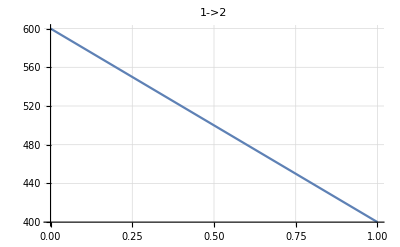
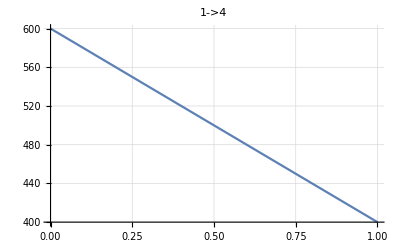
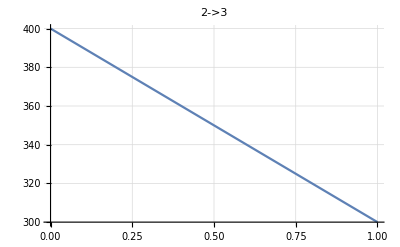
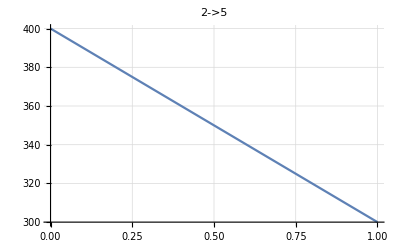
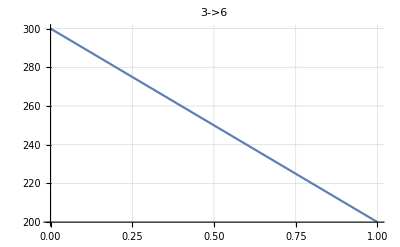
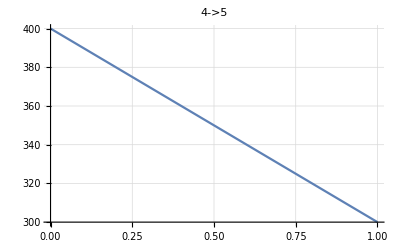
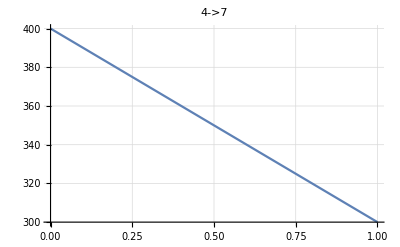
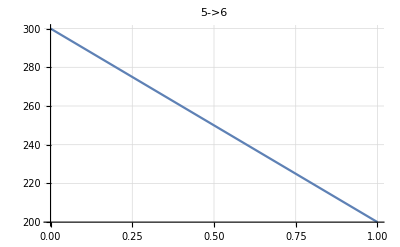

```mathematica
plotU[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
plotM[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
```

```mathematica
AbsoluteTiming[Simplify[And@@listed]]
```

```mathematica
{206.265473,sdfsdfsdfsdf}
```